```mathematica
Clear["Global`*"]
```

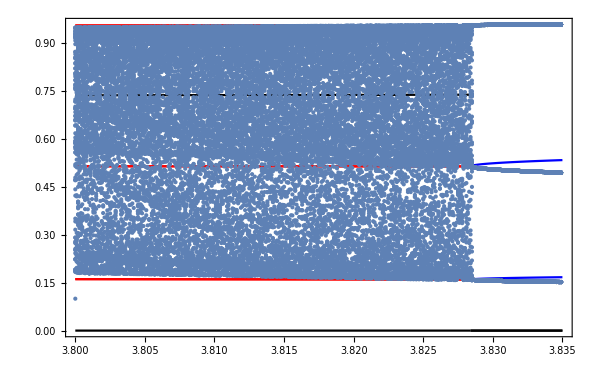

```mathematica
listpointsxy={}
listpointsxμT = {}
(* valores de mu na lista total*)
For[μ = 3.8, μ<3.8284,μ=μ+0.001;
listpointsxμlocal = {};
x = 0.99;
y =1. 10^-10;
AppendTo[listpointsxy,{x, y}];
(* definicao do n de iteracoes *)
if=50000;
For[i=1,i<if,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x, y}];
(* condicao para reduzir valores *)
If[y^2<10^-10,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,x],
Null],
i=if]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμT, listpointsxμlocal]]
```

{}

{}

General::munfl: (-7.93522×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.83829×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.94035×10^-78)^4 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

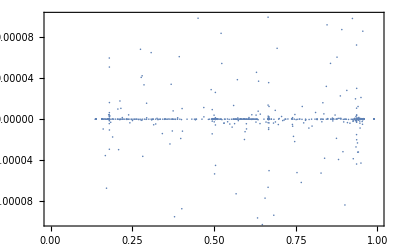

```mathematica
ListPlot[listpointsxy,PlotRange->{{0,1},{-10^-4,10^-4}},Frame->True]
```

```mathematica
Length[listpointsxy]
```

50864

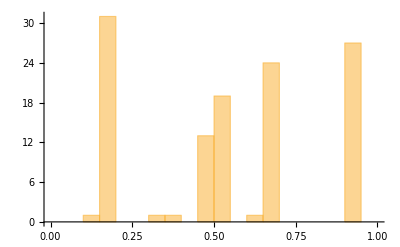
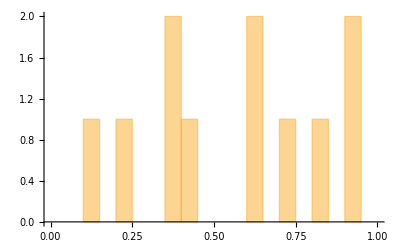
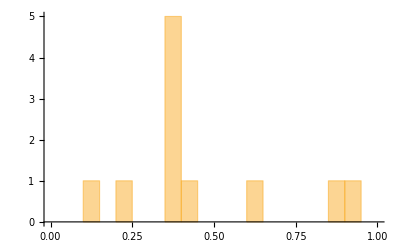
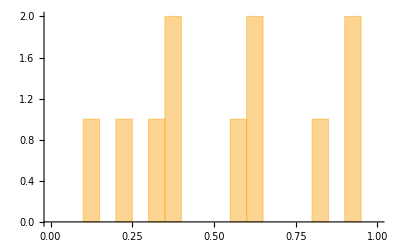
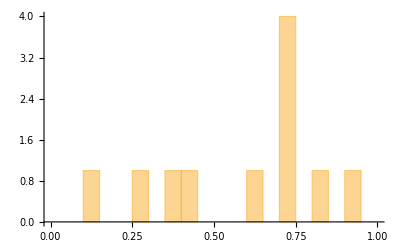
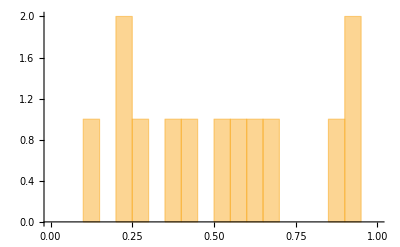
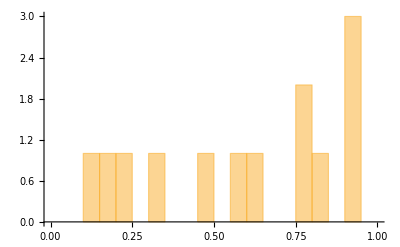
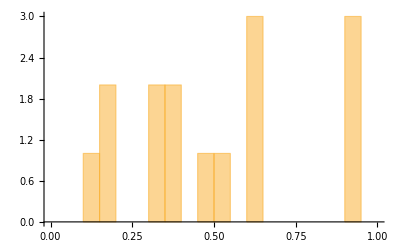

```mathematica
Table[Histogram[{Flatten[listpointsxμT⟦i⟧]},{0,1,5 10^-2}],{i,1,29}]
```

```mathematica
listpointsxy={};
listpointsxμTIndex = {};
listpointsxμT = {};
For[μ = 3.820, μ<3.830,μ=μ+0.00025;
listpointsxμlocal = {};
AppendTo[listpointsxμlocal, μ];
(* valores de 0 a 1 a serem testados para x*)

For[j=2,j< 3 10^1,j++,
x=(j-1)1/(3 10^1);
For[k=-1,k≤ 1,k++,
y = k 10^-1;
α=1;
AppendTo[listpointsxy,{x,α y,0}];
if=500;
(* definicao do n de iteracoes *)
For[i=1,i<if,i++,
(* condicao de estabilidade *)
If[x^2+y^2≤ 1,
(* processo de iteracao *)
x=x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
y = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
AppendTo[listpointsxy,{x,α y,0}];
(* condicao para reduzir valores *)
If[y^2<10^-12,
(* adicao dos valores de x para um unico mu a uma lista *)
AppendTo[listpointsxμlocal,{x}],
Null],
i=if]]]];
(* adicao das listas contendo os valores de x para diferentes mu's em uma unica lista *)
AppendTo[listpointsxμTIndex, Flatten[listpointsxμlocal]]]

For[i = 0, i <Length[listpointsxμTIndex], i++;
local = Delete[listpointsxμTIndex⟦i⟧,1];
AppendTo[listpointsxμT,local]]

listpointsx = listpoints⟦All,2 ;;⟧;
```

```mathematica
x = 0.1;
listpoints = {};
j=1;
For[μ = 3.8, μ<3.830,μ=μ+0.0001,
For[i=1,i<500,i++,
x = μ x(1-x)
];
AppendTo[listpoints,{μ}];
For[i=1,i<5000,i++,
x =μ x(1-x);
AppendTo[listpoints⟦j⟧,x];
];
j++;
]

listpointsx = listpoints⟦All,2 ;;⟧;
```

```mathematica
tempfile = FileNameJoin[{$TemporaryDirectory, "test.wl"}]
```

/private/var/folders/j4/2c2cfr0s369f2xwnypbvrl6h0000gn/T/test.wl

```mathematica
Save[tempfile, {listpoints,listpointsx}]
```

```mathematica
Get[tempfile]
```

{1}
 |  |  |  |

```mathematica
3
```

```mathematica
listpoints⟦1⟧;
```

```mathematica
listpoints⟦1⟧;
```

```mathematica
Length[listpointsxμTIndex⟦1⟧] - Length[listpointsxμT⟦1⟧]
```

1

```mathematica
Length[listpointsxy]
```

32654

```mathematica
Length[listpointsxμT]
```

40

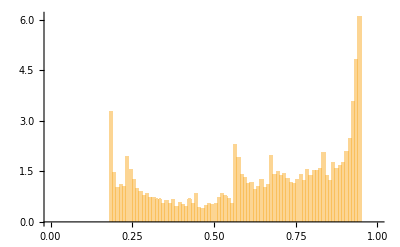
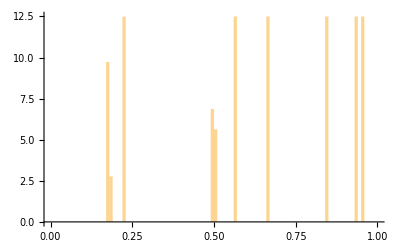
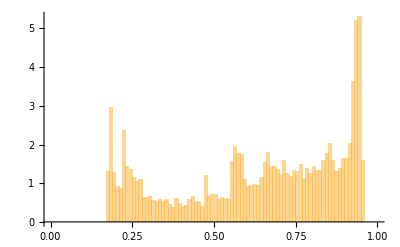
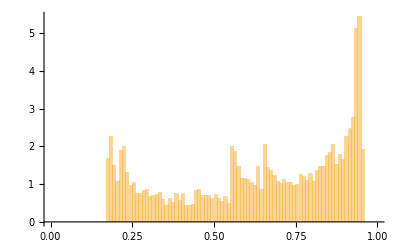
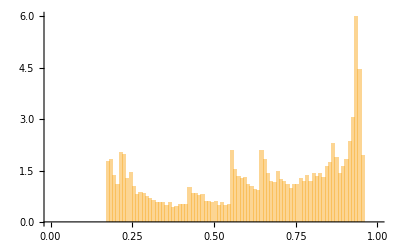
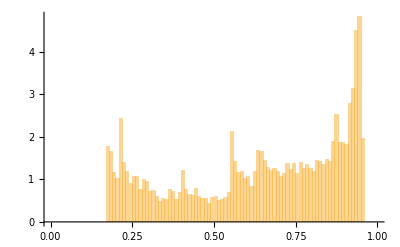
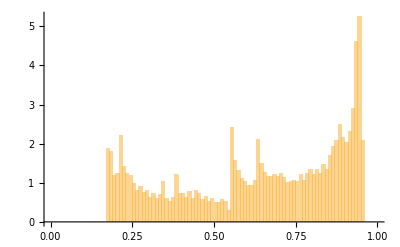
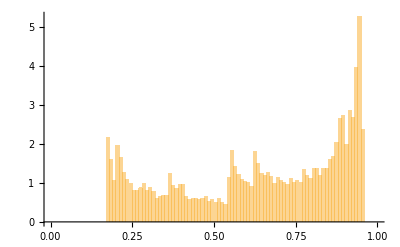
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[{Flatten[listpoints⟦i⟧]},{0,1,1 10^-2}, "PDF"],{i,1,Length[listpoints]} ]
```

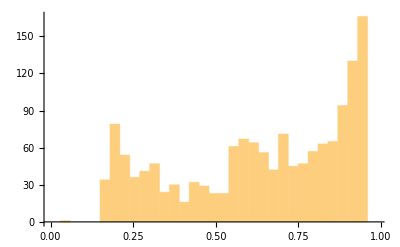

```mathematica
h =Histogram[Flatten[listpointsxμT⟦10⟧],{0,1,3 10^-2}]
```

```mathematica
HL=HistogramList[listpointsxμT⟦10⟧,{0,1,3 10^-2}]
```

{{0,3/100,3/50,9/100,3/25,3/20,9/50,21/100,6/25,27/100,3/10,33/100,9/25,39/100,21/50,9/20,12/25,51/100,27/50,57/100,3/5,63/100,33/50,69/100,18/25,3/4,39/50,81/100,21/25,87/100,9/10,93/100,24/25,99/100},{0,0,0,0,0,135,68,45,41,27,18,25,19,17,19,16,20,106,74,60,42,31,43,31,42,49,48,53,51,63,83,271,0}}

```mathematica
gaus3[xn_]=A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2];
```

O código abaixo não é relevante para os objetivos atuais, fiz ele apenas por confusão. Mas acho que pode vir a ser útil dependendo dos problemas que vamos encontrar.

```mathematica
(*cuttingvalues1 ={};
cuttingvalues2 ={};
flatlist = Sort[{Flatten[listpointsxμT⟦25⟧]}];
For[i=0,i≤ Length[flatlist⟦1⟧] - 1,i++;
j = flatlist⟦1,i⟧;
If[0.305> j>0.3,AppendTo[cuttingvalues1,i],j];
If[0.805> j>0.8,AppendTo[cuttingvalues2,i],j]]

cut1 = Min[cuttingvalues1];
cut2 = Min[cuttingvalues2];

flatlist1 = flatlist[[;;cut1]];
flatlistlocal = flatlist[[cut1;;]];
flatlist2 = flatlistlocal[[;;cut3]];
flatlist3 = flatlistlocal[[cut3;;]];*)
```

pointshl -->  Lista com os pontos mais altos de cada coluna do histograma no formato {{ x1, y1 }, { x2, y2 }, ... }
peaks --> O FindPeaks foi usado para encontrar os picos do histograma. O fator σ  =  2  foi suficiente para isolar os 3 picos desejados.
indexes -->  Lista com os índices de cada pico
Finalmente igualamos {x1, x2, x3} aos valores encontrados para os picos.

```mathematica
pointshl =Partition[Riffle[HL⟦1⟧,HL⟦2⟧],2];
peaks  = FindPeaks[HL⟦2⟧,2];
indexes = peaks[[All,1]]
{x1,x2,x3} = {HL⟦1,indexes⟦1⟧⟧,HL⟦1,indexes⟦2⟧⟧,HL⟦1,indexes⟦3⟧⟧}
```

{6,18,32}

{3/20,51/100,93/100}

Finalmente, tentativa de usar NonlinearModelFit para encontrar os coeficientes desejados. 
Falha na convergência.

Como proceder?

```mathematica
nlm=NonlinearModelFit[pointshl,A1 Exp[α (xn-x1)^2]+A2 Exp[α (xn-x2)^2]+A3 Exp[α(xn-x3)^2],{A1,A2,A3,α },xn]
Plot[nlm[x],{x,0,1}]
```

NonlinearModelFit::ivar: 1 is not a valid variable.

NonlinearModelFit[{{0,0},{3/100,1},{3/50,0},{9/100,0},{3/25,0},{3/20,34},{9/50,79},{21/100,54},{6/25,36},{27/100,41},{3/10,47},{33/100,24},{9/25,30},{39/100,16},{21/50,32},{9/20,29},{12/25,23},{51/100,23},{27/50,61},{57/100,67},{3/5,64},{63/100,56},{33/50,42},{69/100,71},{18/25,45},{3/4,47},{39/50,57},{81/100,63},{21/25,65},{87/100,94},{9/10,130},{93/100,166},{24/25,0}},A3 ⅇ^((-93/100+xn)^2)+A2 ⅇ^((-57/100+xn)^2)+A1 ⅇ^((-9/50+xn)^2),{A1,A2,A3,1},xn]

NonlinearModelFit::ivar: 1. is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[α]
```

{A1→6.52721×10^27,A2→1.18987×10^31,A3→2.53549×10^31,α1→-33.0677,α2→-3280.66,α3→-3483.28}

General::munfl: Exp[-1065.81] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3012.56] is too small to represent as a normalized machine number; precision may be lost.

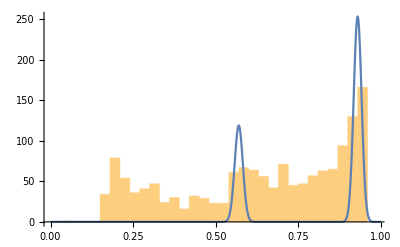

```mathematica
fitgaussian = FindFit[pointshl,{A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2], {α1<0,α2<0,α3<0}},{A1,A2,A3, α1,α2,α3},xn]
Show[h ,Plot[10^-29(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2])/.fitgaussian,{xn,0,1},PlotRange->All]]
```

Apesar de parecer interessante, o SmoothHistogram apresenta resultados abruptamente diferentes ao alterar o fator da função de 0.6994 para 0.6995
Não resulta muito bem na curva que queríamos.

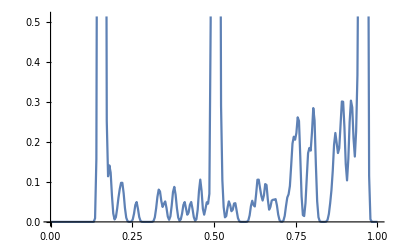

```mathematica
SmoothHistogram[Flatten[listpointsxμT⟦30⟧],0.005, "PDF", PlotRange->{{0,1},Automatic}]
```

Em compensação, uma mera interpolação do conjunto de pontos mais altos da coluna do histograma (pointshl, definido acima), foi suficiente para encontrar um comportamento satisfatório.

InterpolatingFunction[…]

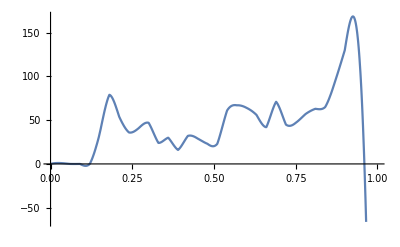

```mathematica
fhl = Interpolation[pointshl, Method->"Hermite"]
Plot[fhl[x],{x,0,1}]
```

Processo quase inteiramente automatizado, faltando somente a função das 3 gaussianas.

```mathematica
ptslencol = {}
For[ i=0, i< Length[listpointsxμT], i++;
HLlocal=HistogramList[Flatten[listpointsxμT⟦i⟧],{0,1,3 10^-2}];
pointshllocal =Partition[Riffle[HLlocal⟦1⟧,HLlocal⟦2⟧],2];
peakslocal  = FindPeaks[HLlocal⟦2⟧,2];
indexeslocal = peakslocal[[All,1]];
{x1l,x2l,x3l} = {HLlocal⟦1,indexes⟦1⟧⟧,HLlocal⟦1,indexes⟦2⟧⟧,HL⟦1,indexes⟦3⟧⟧};
fhllocal = Interpolation[pointshl];
nlmlocal= 0;
fproduto = fhllocal - nlmlocal;
peaksfinal = FindPeaks[fproduto,2];
indexesfinal = peaksfinal[[All,1]];
{x4l,x5l} = {HLlocal⟦1,indexesfinal⟦1⟧⟧,HLlocal⟦1,indexesfinal⟦2⟧⟧};
AppendTo[ptslencol,{x1l,x2l,x3l,x4l,x5l}]]
```

Do que foi proposto, eu consegui apenas:
-  Encontrar x1, x2 e x3
-  Encontrar a função interpolada

O que eu não consegui:
-  Encontrar os coeficientes para gauss3

Próximos passos:
-  Com os coeficientes, fazer a subtração entre a função interpolada e gauss3. Com isso encontramos o x4 e o x5, os picos menos expressivos (para o caso particular do listpointsxμT⟦25⟧)
-  Automatizar o processo (quase pronto) a fim de fazer isso para os outros valores de μ dentro da listpointsxμT, e observar com x1, x2, x3, x4, x5 variam com μ.

```mathematica
σ =  0.9
listμpeak = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = Round[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak,{listpointsxμTIndex⟦i,1⟧,x1}]]

listμpeak2 = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = IntegerPart[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak2,{listpointsxμTIndex⟦i,1⟧,x2}]]

listμpeak3 = {}
For[ i=0, i<Length[listpointsxμT],i++;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,σ];
indexesl = IntegerPart[peaksl[[All,1]]];
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧};
AppendTo[listμpeak3,{listpointsxμTIndex⟦i,1⟧,x3}]]
```

0.9

{}

{}

{}

```mathematica
listμpeak
```

{{3.8205,9/50},{3.821,3/20},{3.8215,9/50},{3.822,3/20},{3.8225,3/20},{3.823,3/20},{3.8235,3/20},{3.824,3/20},{3.8245,3/20},{3.825,3/20},{3.8255,3/20},{3.826,3/20},{3.8265,3/20},{3.827,3/20},{3.8275,3/20},{3.828,3/20},{3.8285,3/20},{3.829,3/20},{3.8295,3/20},{3.83,3/20}}

8007.4-4184.99 z+546.822 z^2

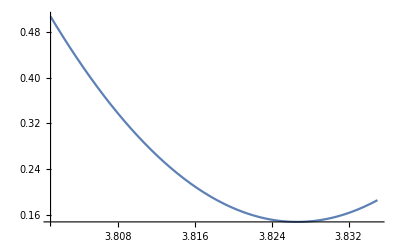

```mathematica
peakμf = Fit[listμpeak, {1,z,z^2},z]
Plot[peakμf,{z,3.801,3.835}]
```

35.5517-9.15789 z

-13.4276+3.74436 z

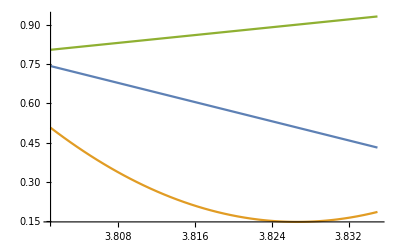

```mathematica
peakμf2 = Fit[listμpeak2,{1,z},z]
peakμf3 = Fit[listμpeak3, {1,z},z]
Plot[{peakμf2,peakμf, peakμf3},{z,3.801,3.835}, PlotRange->All]
```

```mathematica
i = 3;
HLlocal = HistogramList[listpointsxμT⟦i⟧,{0,1,3 10^-2}];
peaksl  = FindPeaks[HLlocal⟦2⟧,1.5]
indexesl = peaksl[[All,1]]
{x1,x2,x3} = {HLlocal⟦1,indexesl⟦1⟧⟧,HLlocal⟦1,indexesl⟦2⟧⟧,HLlocal⟦1,indexesl⟦3⟧⟧}
```

{{8,79},{19,70},{32,196}}

{8,19,32}

{21/100,27/50,93/100}

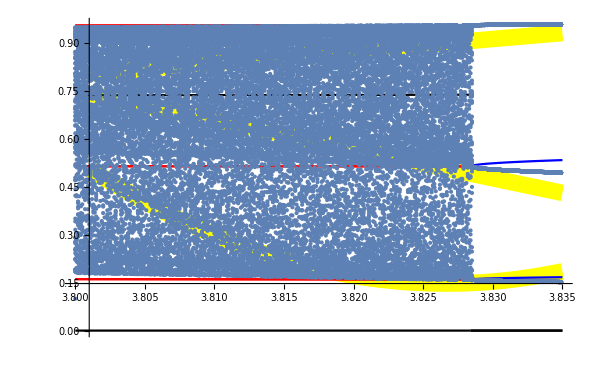

```mathematica
Show[Plot[{peakμf2,peakμf, peakμf3},{z,3.801,3.835}, PlotRange->All, PlotStyle->Directive[Thickness[0.02],Yellow]],-Graphics-]
```

```mathematica
Clear[HLlocal]
```

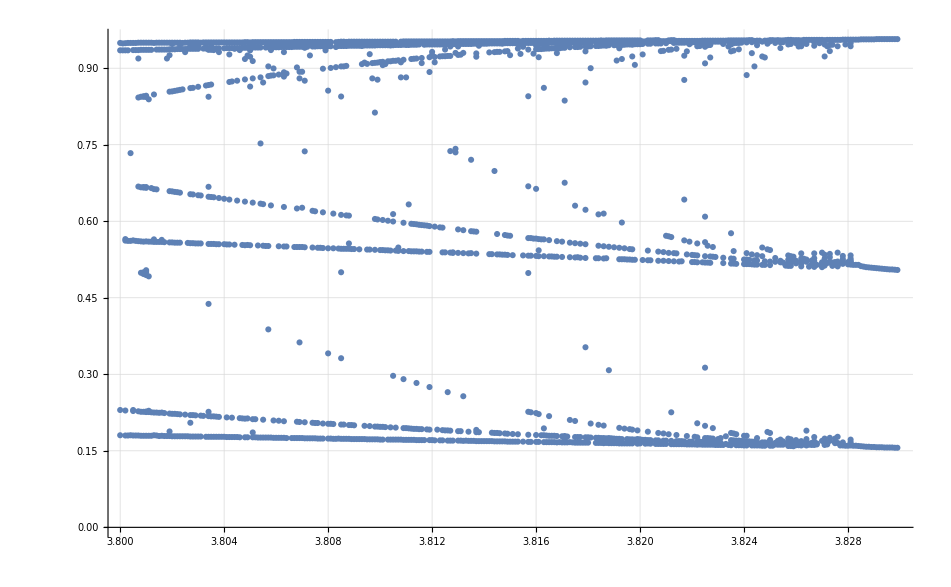

```mathematica
σ = 1.3;
s = 0.9;
t = 3.0;
listμpeakTotal = {};
For[ i=0, i< Length[listpointsx],i++;
HLlocal = HistogramList[listpointsx⟦i⟧,{0,1,5 10^-4}, "PDF"];
peaksl  = FindPeaks[HLlocal⟦2⟧, σ, s, t];
indexesl = Round[peaksl[[All,1]]];
AppendTo[listμpeakTotal,{}];
AppendTo[listμpeakTotal⟦i⟧,listpoints⟦i,1⟧];
For[j=0,j <Length[indexesl], j++;
AppendTo[listμpeakTotal⟦i⟧,HLlocal⟦1,indexesl⟦j⟧⟧]]]
listμpeakTotalp = {};
For[k=0, k<Length[listμpeakTotal],k++;
For[n=1, n<Length[listμpeakTotal⟦k⟧],n++;
AppendTo[listμpeakTotalp,{listμpeakTotal⟦k,1⟧,listμpeakTotal⟦k,n⟧}]]]

ListPlot[listμpeakTotalp, GridLines->Automatic]
```

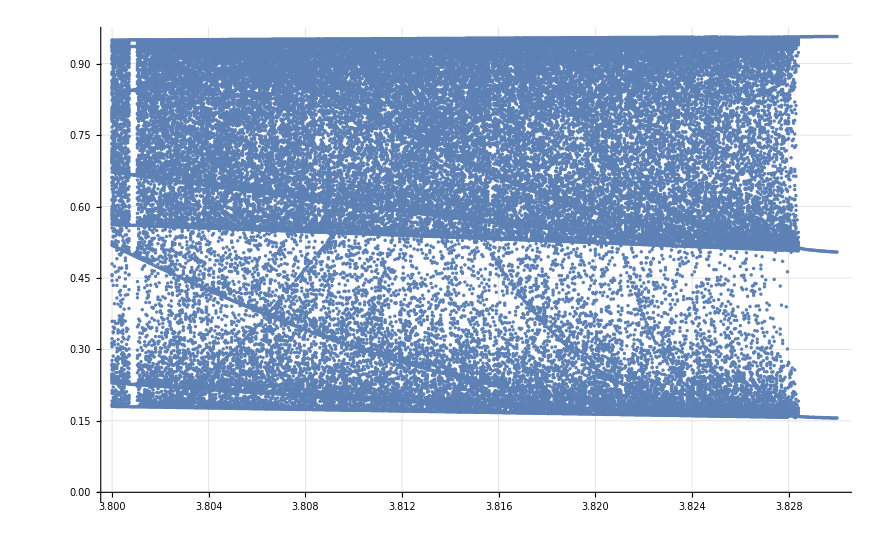

```mathematica
ListPlot[listμpeakTotalp, GridLines->Automatic]
```

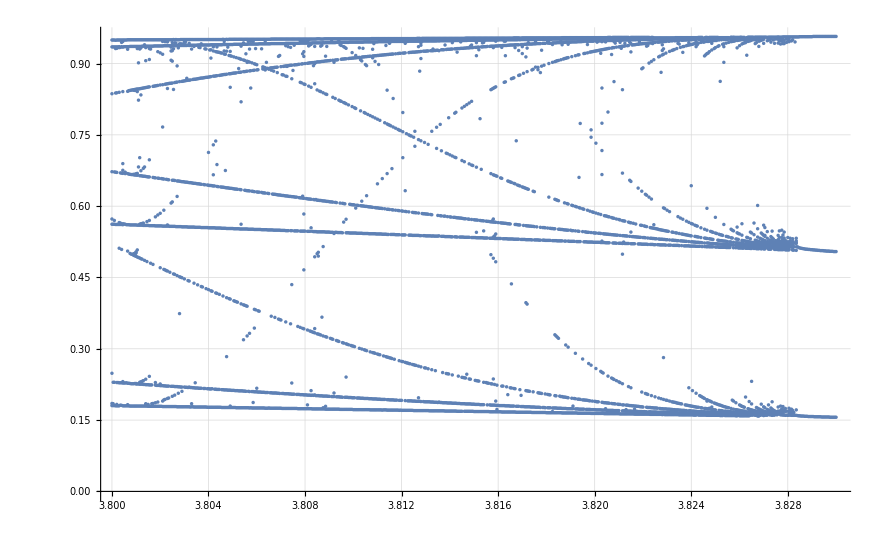

```mathematica
ListPlot[listμpeakTotalp, GridLines->Automatic]
```

```mathematica
For[i=0, i≤  Length[listμpeakTotalp], i++;
curva2step = Select[listμpeakTotalp⟦i⟧, #⟦1⟧ < 3.820 &];
curva2 = Select[curva2step⟦i⟧, 0.52 < #⟦2⟧ < 0.56 &]]
```

Part::partd: Part specification 3.8⟦1⟧ is longer than depth of object.

Part::partd: Part specification 361/2000⟦1⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

```mathematica
curva2step = Select[listμpeakTotalp, #⟦1⟧ < 3.817 &];
curva2step2 = Select[curva2step, 0.52 < #⟦2⟧ < 0.56 &];
curva2 = DeleteDuplicates[curva2step2, #1⟦1⟧ == #2⟦1⟧ &]
```

{{3.8013,1119/2000},{3.8014,1119/2000},{3.8015,1119/2000},{3.8016,1119/2000},{3.8017,559/1000},{3.8019,1117/2000},{3.802,1117/2000},{3.8021,279/500},{3.8022,279/500},{3.8023,279/500},{3.8026,223/400},{3.8027,557/1000},{3.8028,557/1000},{3.8029,1113/2000},{3.803,1113/2000},{3.8031,1113/2000},{3.8034,1111/2000},{3.8035,1111/2000},{3.8036,1111/2000},{3.8037,111/200},{3.8038,111/200},{3.804,111/200},{3.8041,1109/2000},{3.8042,1109/2000},{3.8044,277/500},{3.8047,1107/2000},{3.8048,553/1000},{3.8049,1107/2000},{3.805,553/1000},{3.8053,221/400},{3.8055,69/125},{3.8056,1103/2000},{3.8057,1103/2000},{3.8061,551/1000},{3.8063,1101/2000},{3.8064,1101/2000},{3.8067,1099/2000},{3.8068,1099/2000},{3.8069,1099/2000},{3.807,1099/2000},{3.8071,549/1000},{3.8074,1097/2000},{3.8076,137/250},{3.8077,137/250},{3.8078,219/400},{3.808,547/1000},{3.8082,547/1000},{3.8084,1093/2000},{3.8085,273/500},{3.8086,273/500},{3.8087,273/500},{3.8088,273/500},{3.8089,1091/2000},{3.809,1091/2000},{3.8092,109/200},{3.8095,1089/2000},{3.8096,1089/2000},{3.8098,68/125},{3.81,1087/2000},{3.8101,1087/2000},{3.8102,543/1000},{3.8103,543/1000},{3.8104,217/400},{3.8106,217/400},{3.8107,271/500},{3.8109,1083/2000},{3.8111,1083/2000},{3.8112,541/1000},{3.8113,541/1000},{3.8114,541/1000},{3.8115,1081/2000},{3.8116,1081/2000},{3.8118,27/50},{3.8119,27/50},{3.8124,539/1000},{3.8125,539/1000},{3.8127,1077/2000},{3.8128,269/500},{3.813,269/500},{3.8132,43/80},{3.8134,537/1000},{3.8135,43/80},{3.8137,1073/2000},{3.8142,1071/2000},{3.8143,1071/2000},{3.8145,107/200},{3.8146,107/200},{3.8147,1069/2000},{3.8148,1069/2000},{3.8149,267/500},{3.8151,1067/2000},{3.8155,533/1000},{3.8157,213/400},{3.8158,213/400},{3.816,133/250},{3.8161,1063/2000},{3.8163,1063/2000},{3.8165,531/1000},{3.8166,531/1000},{3.8167,1061/2000},{3.8168,1061/2000}}

```mathematica
curva2f = Interpolation[curva2, Method->"Hermite"]
```

```mathematica
InterpolatingFunction[…]
```

```mathematica
Clear[a,b, x]
```

```mathematica
coef = FindFit[curva2, a x^2 + b x + c, {a,b, c},x]
```

{a→-4.06013,b→29.0461,c→-51.1848}

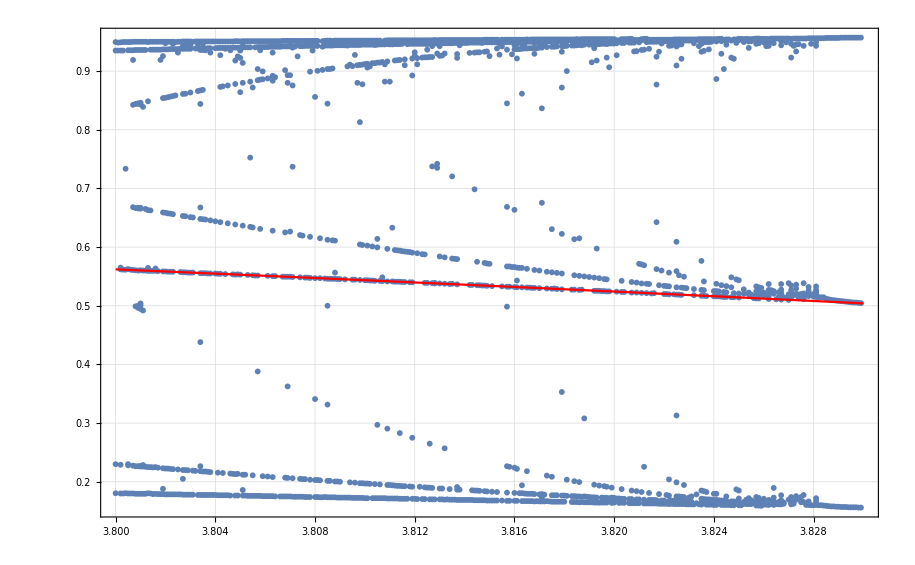

```mathematica
Show[ListPlot[listμpeakTotalp],Plot[ a x^2 + b x + c/.coef, {x, 3.800, 3.830}, PlotStyle->Red], Frame-> True, GridLines-> Automatic, PlotRange-> Automatic]
```

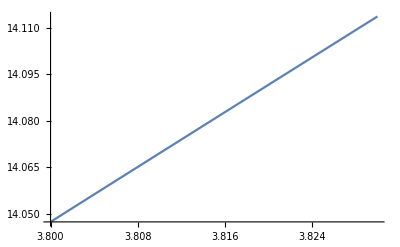

```mathematica
Plot[ a x^2 + b x + c/.coef, {x, 3.800, 3.830}]
```

```mathematica
listμpeakTotalp;
```

```mathematica
listpoints⟦1⟧;
```

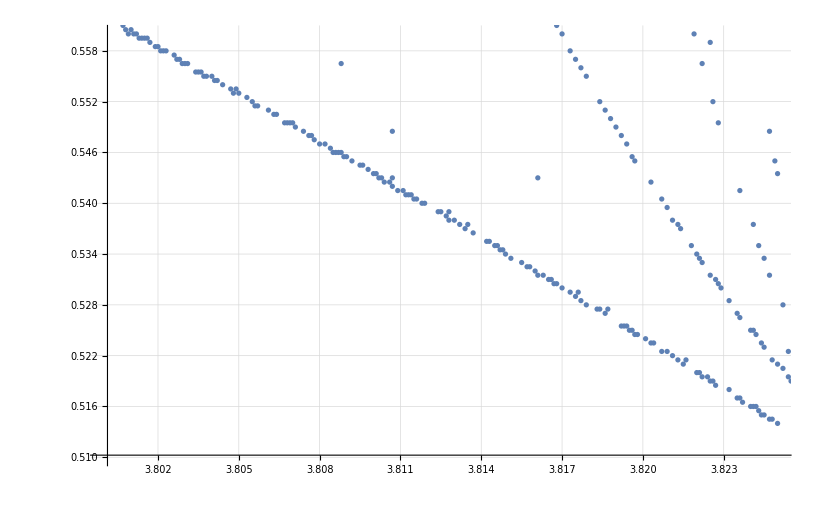

```mathematica
ListPlot[listμpeakTotalp, GridLines->Automatic, PlotRange->{{3.800,3.825},{0.51,0.56}}]
```

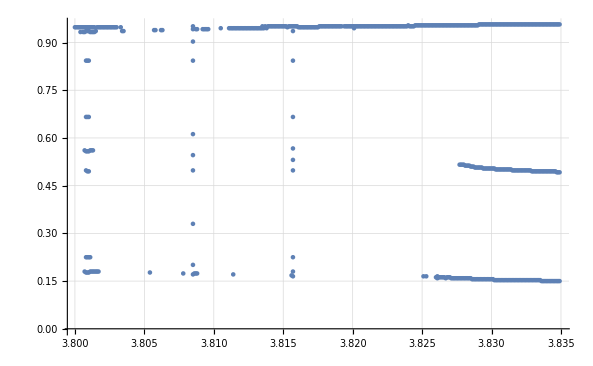

{{8.,15.8651},{17.,0.1002},{26.,15.9319},{33.,0.1002},{38.,0.267201},{48.,15.9653}}

```mathematica
ListPlot[listμpeakTotalp, GridLines->Automatic]
```

```mathematica
HisT2=Table[Histogram[{Flatten[listpointsx⟦i⟧]},{0,1,3 10^-3}],{i,1,Length[listpointsx]}];
```

```mathematica
fitL={};
For[j=1,j≤Length[listpointsx],j++,
HL=HistogramList[listpointsx⟦j⟧,{0,1,3 10^-3}];
pointshl =Partition[Riffle[HL⟦1⟧,HL⟦2⟧],2];
peaks  = FindPeaks[HL⟦2⟧,0.8, 0.7, 0.9];
indexes = Round[peaks⟦All,1⟧];
{x1,x2,x3} = {HL⟦1,indexes⟦1⟧⟧,HL⟦1,indexes⟦2⟧⟧,957/1000};
AppendTo[fitL,FindFit[pointshl,{A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+ Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2], {α1<-10^3,α2<-10^3,α3<-10^3,α4<-10^2,α5<-10^2,A1>0,A2>0,0<A4,0<A5,x2<x4<x3,x1<x5<x2}},{A1,A2,A4, A5,α1,α2,α3,α4,α5,x4,x5},xn]]
(*Show[h ,Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitgaussian,{xn,0,1},PlotRange->All],Frame-> True]
*)]
```

FindFit::acceptlev: Solved to acceptable level.

General::stop: Further output of FindFit::acceptlev will be suppressed during this calculation.

FindFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.11821×10^-12,1.17378,2.69971×10^-13}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.01491×10^-13,0.000984209,7.01317×10^-14}, is returned.

FindFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {3.49824×10^-13,0.0632031,7.38618×10^-14}, is returned.

General::stop: Further output of FindFit::eit will be suppressed during this calculation.

```mathematica
x3
```

957/1000

General::munfl: Exp[-4574.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-915.81] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5944.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

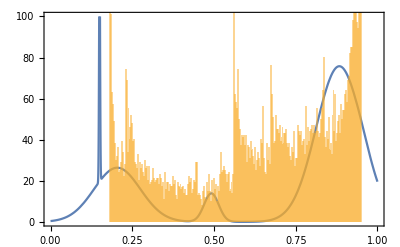
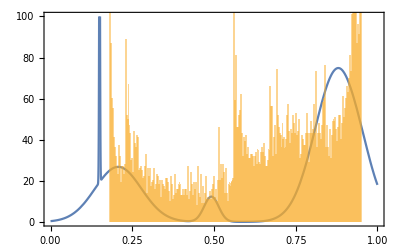
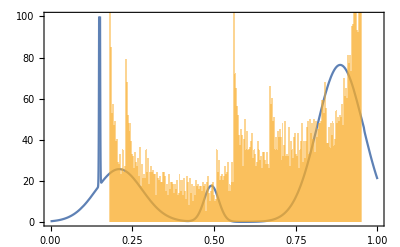
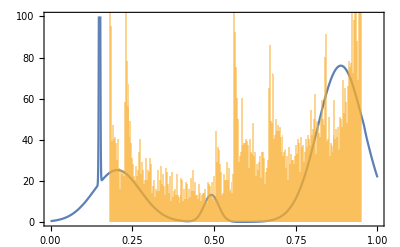
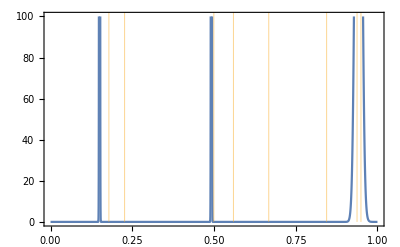
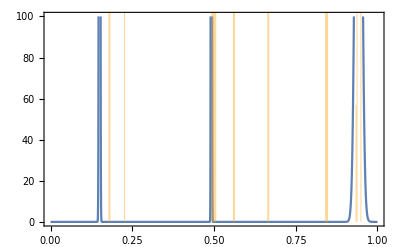
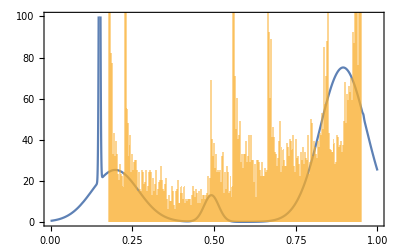
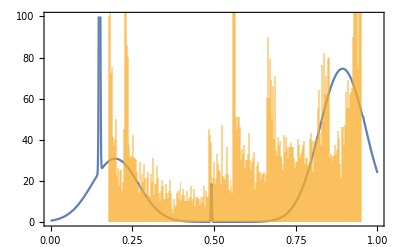
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+ Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitL⟦j⟧,{xn,0,1},Frame->True, PlotRange->{0,100}],HisT2⟦j⟧],{j,1,Length[fitL]}]
```

```mathematica
fitL⟦1⟧
```

{A1→115.734,A2→2.50324×10^-7,A3→17.4074,A4→26.7282,A5→1.0122×10^-7,α1→-183027.,α2→-1754.46,α3→-1000.,α4→-100.,α5→-827.604,x4→0.216,x5→0.195631}

```mathematica
Show[Plot[(A1 Exp[α1 (xn-x1)^2]+A2 Exp[α2 (xn-x2)^2]+A3 Exp[α3 (xn-x3)^2]+A4 Exp[α4 (xn-x4)^2]+A5 Exp[α5 (xn-x5)^2])/.fitL⟦1⟧,{xn,0,1},Frame->True],HisT2⟦1⟧]
```

General::munfl: Exp[-4116.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-915.81] is too small to represent as a normalized machine number; precision may be lost.